```mathematica
Exit[]
```

```mathematica
t[2,x_]:=ChebyshevT[2,x];t[3,x_]:=ChebyshevT[3,x];
k[n_,x_,b_]:=b*t[n,x]+(1-b)*x;
f[{n_,b_,s_},a_,{x_,y_,z_}]:=(t[n,y]+a*Mean[{s*k[n,x,b]-t[n,y],s*k[n,z,b]-t[n,y]}]);

f2Ap[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{2,1,+1},a,{x,y,z}]},v,p];
f2Am[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{2,1,-1},a,{x,y,z}]},v,p];
f2Bp[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{2,0,+1},a,{x,y,z}]},v,p];
f2Bm[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{2,0,-1},a,{x,y,z}]},v,p];
f3Ap[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{3,1,+1},a,{x,y,z}]},v,p];
f3Am[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{3,1,-1},a,{x,y,z}]},v,p];
f3Bp[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{3,0,+1},a,{x,y,z}]},v,p];
f3Bm[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{3,0,-1},a,{x,y,z}]},v,p];
```

{2025,5,1,19,44,50.31291}

{2025,5,1,19,45,57.815213}

1.1250384 minutes

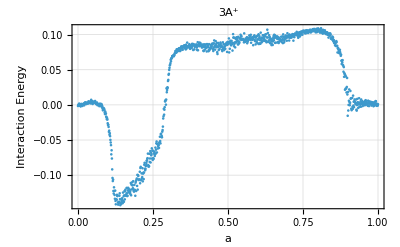

{{0.,-0.00157215},{0.001,-0.000619103},{0.002,0.000576242},{0.003,0.000138637},{0.004,0.00185243},{0.005,-0.000947614},{0.006,-0.000414177},{0.007,-0.000487784},{0.008,-0.00152618},{0.009,-0.00220848},{0.01,0.0011969},{0.011,0.000530638},{0.012,-0.000850688},{0.013,0.0013932},{0.014,-1.85961×10^-6},{0.015,-0.00148868},{0.016,0.000132748},{0.017,0.00076769},{0.018,0.000621035},{0.019,0.00107292},{0.02,0.00200305},{0.021,-0.00059194},{0.022,0.00272999},{0.023,0.00287125},{0.024,0.00295059},{0.025,0.00360547},{0.026,0.00210075},{0.027,0.00151412},{0.028,0.00121058},{0.029,0.00310176},{0.03,0.00246577},{0.031,0.00203562},{0.032,0.0033396},{0.033,0.00210975},{0.034,0.00237128},{0.035,0.00508463},{0.036,0.0026776},{0.037,0.00331437},{0.038,0.00268005},{0.039,0.00409417},{0.04,0.00321874},{0.041,0.00468457},{0.042,0.00474471},{0.043,0.00200587},{0.044,0.00724823},{0.045,0.00524759},{0.046,0.00509381},{0.047,0.00467512},{0.048,0.00515718},{0.049,0.00127864},{0.05,0.00415807},{0.051,0.00306171},{0.052,0.00434504},{0.053,0.00309278},{0.054,0.0033706},{0.055,0.00340391},{0.056,0.00297442},{0.057,0.00555877},{0.058,0.00300259},{0.059,0.00219879},{0.06,0.00116474},{0.061,0.00231296},{0.062,0.00272089},{0.063,0.00342817},{0.064,0.00101096},{0.065,-0.000475885},{0.066,0.000823183},{0.067,0.000640174},{0.068,0.00105676},{0.069,0.000991756},{0.07,0.00146267},{0.071,-0.00182396},{0.072,0.000299418},{0.073,0.000557933},{0.074,0.0016895},{0.075,-0.000580048},{0.076,-0.00166917},{0.077,-0.00112065},{0.078,0.00122569},{0.079,0.0000571518},{0.08,-0.00349088},{0.081,-0.00181179},{0.082,-0.00520926},{0.083,-0.0077582},{0.084,-0.00579204},{0.085,-0.00443995},{0.086,-0.00699255},{0.087,-0.00536145},{0.088,-0.00717306},{0.089,-0.0109097},{0.09,-0.013109},{0.091,-0.00952892},{0.092,-0.0126452},{0.093,-0.0121658},{0.094,-0.016667},{0.095,-0.0175738},{0.096,-0.0203976},{0.097,-0.0189623},{0.098,-0.0209157},{0.099,-0.0261404},{0.1,-0.0285079},{0.101,-0.0281943},{0.102,-0.031331},{0.103,-0.0383164},{0.104,-0.0366833},{0.105,-0.0425111},{0.106,-0.0403301},{0.107,-0.0445436},{0.108,-0.0497872},{0.109,-0.0535177},{0.11,-0.0573111},{0.111,-0.0703908},{0.112,-0.0646255},{0.113,-0.0763347},{0.114,-0.0917914},{0.115,-0.103983},{0.116,-0.108387},{0.117,-0.106282},{0.118,-0.122525},{0.119,-0.126185},{0.12,-0.117302},{0.121,-0.122514},{0.122,-0.128233},{0.123,-0.133586},{0.124,-0.121973},{0.125,-0.136637},{0.126,-0.141477},{0.127,-0.134486},{0.128,-0.134691},{0.129,-0.134979},{0.13,-0.127916},{0.131,-0.129874},{0.132,-0.128775},{0.133,-0.138928},{0.134,-0.141987},{0.135,-0.138716},{0.136,-0.139218},{0.137,-0.137753},{0.138,-0.129295},{0.139,-0.125832},{0.14,-0.134055},{0.141,-0.142716},{0.142,-0.139647},{0.143,-0.13998},{0.144,-0.140884},{0.145,-0.136653},{0.146,-0.134306},{0.147,-0.132809},{0.148,-0.135543},{0.149,-0.139858},{0.15,-0.12477},{0.151,-0.136833},{0.152,-0.130109},{0.153,-0.137886},{0.154,-0.128742},{0.155,-0.122645},{0.156,-0.134435},{0.157,-0.12306},{0.158,-0.120583},{0.159,-0.129113},{0.16,-0.127474},{0.161,-0.12929},{0.162,-0.118098},{0.163,-0.125613},{0.164,-0.129786},{0.165,-0.129223},{0.166,-0.121825},{0.167,-0.117962},{0.168,-0.118955},{0.169,-0.124037},{0.17,-0.120407},{0.171,-0.122346},{0.172,-0.12546},{0.173,-0.120777},{0.174,-0.123715},{0.175,-0.127087},{0.176,-0.111153},{0.177,-0.128631},{0.178,-0.113206},{0.179,-0.120369},{0.18,-0.114059},{0.181,-0.109919},{0.182,-0.114557},{0.183,-0.118515},{0.184,-0.108591},{0.185,-0.120659},{0.186,-0.122822},{0.187,-0.123352},{0.188,-0.1138},{0.189,-0.120749},{0.19,-0.121632},{0.191,-0.129313},{0.192,-0.110645},{0.193,-0.108502},{0.194,-0.122503},{0.195,-0.106443},{0.196,-0.104759},{0.197,-0.115312},{0.198,-0.0995713},{0.199,-0.120572},{0.2,-0.0999689},{0.201,-0.101177},{0.202,-0.106332},{0.203,-0.106972},{0.204,-0.106066},{0.205,-0.106658},{0.206,-0.0951547},{0.207,-0.111517},{0.208,-0.0898576},{0.209,-0.0881891},{0.21,-0.107316},{0.211,-0.106186},{0.212,-0.0974287},{0.213,-0.104495},{0.214,-0.102807},{0.215,-0.0901458},{0.216,-0.10881},{0.217,-0.0978479},{0.218,-0.0964366},{0.219,-0.105593},{0.22,-0.0962349},{0.221,-0.0852496},{0.222,-0.0824517},{0.223,-0.0909494},{0.224,-0.0930608},{0.225,-0.0909952},{0.226,-0.0870803},{0.227,-0.0857893},{0.228,-0.0824801},{0.229,-0.0794476},{0.23,-0.0791124},{0.231,-0.0766005},{0.232,-0.0758038},{0.233,-0.0693801},{0.234,-0.0856566},{0.235,-0.0877929},{0.236,-0.0874744},{0.237,-0.0872244},{0.238,-0.0695454},{0.239,-0.0811626},{0.24,-0.0762786},{0.241,-0.0657247},{0.242,-0.0819331},{0.243,-0.0677595},{0.244,-0.0717621},{0.245,-0.0701287},{0.246,-0.0618537},{0.247,-0.076246},{0.248,-0.064859},{0.249,-0.078254},{0.25,-0.0654911},{0.251,-0.0759619},{0.252,-0.0768284},{0.253,-0.069033},{0.254,-0.0692804},{0.255,-0.0664233},{0.256,-0.0726433},{0.257,-0.0695922},{0.258,-0.0607828},{0.259,-0.0693665},{0.26,-0.0637493},{0.261,-0.0547184},{0.262,-0.0520854},{0.263,-0.0676983},{0.264,-0.0552951},{0.265,-0.0559945},{0.266,-0.062085},{0.267,-0.0587099},{0.268,-0.0565188},{0.269,-0.0571971},{0.27,-0.0612588},{0.271,-0.0536902},{0.272,-0.0534181},{0.273,-0.0453318},{0.274,-0.0514493},{0.275,-0.0547763},{0.276,-0.0415855},{0.277,-0.0411062},{0.278,-0.0456562},{0.279,-0.0441275},{0.28,-0.0461122},{0.281,-0.0380931},{0.282,-0.035828},{0.283,-0.0309318},{0.284,-0.0193679},{0.285,-0.0162593},{0.286,-0.00569333},{0.287,-0.0139435},{0.288,-0.00686938},{0.289,-0.00331191},{0.29,0.00502828},{0.291,0.00522095},{0.292,0.00691387},{0.293,0.000311071},{0.294,0.00752788},{0.295,0.0236263},{0.296,0.0179868},{0.297,0.0212178},{0.298,0.0250666},{0.299,0.0241838},{0.3,0.0339784},{0.301,0.035556},{0.302,0.0428691},{0.303,0.0442179},{0.304,0.04974},{0.305,0.0527664},{0.306,0.0561543},{0.307,0.0570303},{0.308,0.0592848},{0.309,0.0643633},{0.31,0.0620498},{0.311,0.0660256},{0.312,0.0664433},{0.313,0.0665747},{0.314,0.0692733},{0.315,0.0693509},{0.316,0.0698971},{0.317,0.0696995},{0.318,0.0701974},{0.319,0.0690395},{0.32,0.0703246},{0.321,0.0704515},{0.322,0.0727974},{0.323,0.0733101},{0.324,0.074465},{0.325,0.0765525},{0.326,0.0767556},{0.327,0.0742265},{0.328,0.0747142},{0.329,0.0790885},{0.33,0.0765107},{0.331,0.0779029},{0.332,0.0761434},{0.333,0.0793741},{0.334,0.0784},{0.335,0.0771292},{0.336,0.0770927},{0.337,0.0805593},{0.338,0.0806666},{0.339,0.0806193},{0.34,0.0765133},{0.341,0.0789596},{0.342,0.0775694},{0.343,0.0801207},{0.344,0.0828583},{0.345,0.083043},{0.346,0.0823214},{0.347,0.0824176},{0.348,0.0807478},{0.349,0.0783913},{0.35,0.0833342},{0.351,0.0823108},{0.352,0.0828978},{0.353,0.0822061},{0.354,0.0848134},{0.355,0.0838161},{0.356,0.0806995},{0.357,0.0827951},{0.358,0.0847986},{0.359,0.0789938},{0.36,0.0856563},{0.361,0.0796088},{0.362,0.0830889},{0.363,0.0822596},{0.364,0.0886288},{0.365,0.0817599},{0.366,0.0833923},{0.367,0.0820454},{0.368,0.0838032},{0.369,0.0827443},{0.37,0.084416},{0.371,0.0864467},{0.372,0.0822262},{0.373,0.0803923},{0.374,0.0797626},{0.375,0.0818633},{0.376,0.0845993},{0.377,0.0846004},{0.378,0.0818085},{0.379,0.0809733},{0.38,0.0867919},{0.381,0.0837144},{0.382,0.0841382},{0.383,0.0867073},{0.384,0.0780751},{0.385,0.0861333},{0.386,0.08555},{0.387,0.0856034},{0.388,0.0790571},{0.389,0.0826862},{0.39,0.0840739},{0.391,0.0842481},{0.392,0.08459},{0.393,0.083919},{0.394,0.0861156},{0.395,0.0826163},{0.396,0.081454},{0.397,0.078087},{0.398,0.0844903},{0.399,0.0891918},{0.4,0.0777313},{0.401,0.0849148},{0.402,0.0863183},{0.403,0.0859622},{0.404,0.0833929},{0.405,0.0886624},{0.406,0.0859451},{0.407,0.0862178},{0.408,0.0879693},{0.409,0.0838071},{0.41,0.084605},{0.411,0.0849447},{0.412,0.085788},{0.413,0.0815375},{0.414,0.0846067},{0.415,0.0843656},{0.416,0.0857322},{0.417,0.082243},{0.418,0.0771663},{0.419,0.0765234},{0.42,0.0861285},{0.421,0.0828728},{0.422,0.0827314},{0.423,0.0785974},{0.424,0.0860454},{0.425,0.084958},{0.426,0.0806199},{0.427,0.081792},{0.428,0.0813395},{0.429,0.0760164},{0.43,0.0865194},{0.431,0.086169},{0.432,0.0822283},{0.433,0.0843882},{0.434,0.0826694},{0.435,0.0763381},{0.436,0.0780924},{0.437,0.0864271},{0.438,0.0776273},{0.439,0.0794563},{0.44,0.0801887},{0.441,0.0808145},{0.442,0.0853091},{0.443,0.0826265},{0.444,0.0821982},{0.445,0.0806993},{0.446,0.0837431},{0.447,0.086748},{0.448,0.0871229},{0.449,0.0866655},{0.45,0.0790473},{0.451,0.0766285},{0.452,0.0811482},{0.453,0.0876876},{0.454,0.0917038},{0.455,0.0828887},{0.456,0.0840964},{0.457,0.0785706},{0.458,0.0847004},{0.459,0.0906922},{0.46,0.0862844},{0.461,0.0819341},{0.462,0.0844508},{0.463,0.0882663},{0.464,0.0749332},{0.465,0.0723749},{0.466,0.0822491},{0.467,0.0826131},{0.468,0.0880836},{0.469,0.078026},{0.47,0.0855218},{0.471,0.0855595},{0.472,0.0796568},{0.473,0.0833337},{0.474,0.0837472},{0.475,0.0887496},{0.476,0.0866267},{0.477,0.0824487},{0.478,0.0834367},{0.479,0.0823638},{0.48,0.078064},{0.481,0.0765147},{0.482,0.0830798},{0.483,0.0890218},{0.484,0.0798766},{0.485,0.0862661},{0.486,0.0809697},{0.487,0.0779287},{0.488,0.0806602},{0.489,0.0859972},{0.49,0.0833509},{0.491,0.0798067},{0.492,0.0857181},{0.493,0.0861589},{0.494,0.0874375},{0.495,0.0852844},{0.496,0.0887817},{0.497,0.0753341},{0.498,0.0854757},{0.499,0.0869859},{0.5,0.0897964},{0.501,0.0872636},{0.502,0.0868339},{0.503,0.0945358},{0.504,0.0746178},{0.505,0.0891525},{0.506,0.0798206},{0.507,0.0890601},{0.508,0.0912611},{0.509,0.0876237},{0.51,0.08482},{0.511,0.0852589},{0.512,0.0910763},{0.513,0.0871501},{0.514,0.0869606},{0.515,0.0772649},{0.516,0.0882655},{0.517,0.100664},{0.518,0.0956906},{0.519,0.0959776},{0.52,0.0834363},{0.521,0.0864317},{0.522,0.0951484},{0.523,0.0889974},{0.524,0.0818042},{0.525,0.0950948},{0.526,0.0887694},{0.527,0.0932566},{0.528,0.0890327},{0.529,0.0962215},{0.53,0.0907771},{0.531,0.0942483},{0.532,0.0918183},{0.533,0.0859567},{0.534,0.0968588},{0.535,0.0864198},{0.536,0.0890967},{0.537,0.0902588},{0.538,0.0883926},{0.539,0.0944959},{0.54,0.0947108},{0.541,0.0946758},{0.542,0.0997676},{0.543,0.0971873},{0.544,0.0924607},{0.545,0.0977231},{0.546,0.0930425},{0.547,0.0932068},{0.548,0.0936813},{0.549,0.0935903},{0.55,0.0937595},{0.551,0.0934153},{0.552,0.0922253},{0.553,0.0890172},{0.554,0.101746},{0.555,0.0895278},{0.556,0.0908236},{0.557,0.0897071},{0.558,0.0924996},{0.559,0.0945361},{0.56,0.0932826},{0.561,0.0926902},{0.562,0.090984},{0.563,0.0962886},{0.564,0.0876799},{0.565,0.0916364},{0.566,0.0900071},{0.567,0.0950731},{0.568,0.0927746},{0.569,0.0949949},{0.57,0.0934155},{0.571,0.0988778},{0.572,0.0953294},{0.573,0.0971108},{0.574,0.0929895},{0.575,0.0928435},{0.576,0.0997197},{0.577,0.0884106},{0.578,0.0931647},{0.579,0.094425},{0.58,0.0957754},{0.581,0.0961301},{0.582,0.0925044},{0.583,0.0939655},{0.584,0.084926},{0.585,0.0958922},{0.586,0.0974782},{0.587,0.0977606},{0.588,0.0989034},{0.589,0.0925676},{0.59,0.090792},{0.591,0.0963662},{0.592,0.086083},{0.593,0.0956425},{0.594,0.0972733},{0.595,0.0903042},{0.596,0.0888715},{0.597,0.0978803},{0.598,0.0930804},{0.599,0.0876271},{0.6,0.0929339},{0.601,0.099421},{0.602,0.100458},{0.603,0.0865731},{0.604,0.0950619},{0.605,0.0975638},{0.606,0.0875623},{0.607,0.0920039},{0.608,0.087006},{0.609,0.102779},{0.61,0.0946965},{0.611,0.092047},{0.612,0.0888679},{0.613,0.0958595},{0.614,0.0899985},{0.615,0.0946956},{0.616,0.099144},{0.617,0.0912703},{0.618,0.0991733},{0.619,0.0932305},{0.62,0.0967743},{0.621,0.093624},{0.622,0.0911164},{0.623,0.0977171},{0.624,0.100087},{0.625,0.0912481},{0.626,0.091226},{0.627,0.100556},{0.628,0.0891257},{0.629,0.0961173},{0.63,0.089541},{0.631,0.106983},{0.632,0.0958002},{0.633,0.102379},{0.634,0.0897592},{0.635,0.0899696},{0.636,0.0918151},{0.637,0.0991659},{0.638,0.0957835},{0.639,0.0966618},{0.64,0.0878974},{0.641,0.0931893},{0.642,0.0879955},{0.643,0.0942646},{0.644,0.0908478},{0.645,0.0850884},{0.646,0.086461},{0.647,0.093359},{0.648,0.0903655},{0.649,0.0852678},{0.65,0.0905149},{0.651,0.0955306},{0.652,0.0980156},{0.653,0.091974},{0.654,0.0997744},{0.655,0.0951772},{0.656,0.0992223},{0.657,0.0881871},{0.658,0.0969652},{0.659,0.0884527},{0.66,0.0959306},{0.661,0.0958877},{0.662,0.0968911},{0.663,0.097554},{0.664,0.0939786},{0.665,0.0889327},{0.666,0.096713},{0.667,0.0895871},{0.668,0.0938275},{0.669,0.0880323},{0.67,0.0954984},{0.671,0.0900771},{0.672,0.0933355},{0.673,0.0931377},{0.674,0.0932224},{0.675,0.0912688},{0.676,0.0915477},{0.677,0.096919},{0.678,0.0914144},{0.679,0.0894076},{0.68,0.0926985},{0.681,0.0973548},{0.682,0.0936467},{0.683,0.0878771},{0.684,0.10034},{0.685,0.0967266},{0.686,0.0928432},{0.687,0.0888921},{0.688,0.0911511},{0.689,0.0965983},{0.69,0.0945891},{0.691,0.0941682},{0.692,0.0982683},{0.693,0.0986186},{0.694,0.0954961},{0.695,0.0974023},{0.696,0.0912898},{0.697,0.0959613},{0.698,0.101969},{0.699,0.0966248},{0.7,0.097777},{0.701,0.0983766},{0.702,0.0988482},{0.703,0.0959627},{0.704,0.0915822},{0.705,0.100191},{0.706,0.0964506},{0.707,0.0955568},{0.708,0.098907},{0.709,0.0966478},{0.71,0.0958749},{0.711,0.0975466},{0.712,0.0959236},{0.713,0.0987037},{0.714,0.0999167},{0.715,0.10069},{0.716,0.0982472},{0.717,0.099106},{0.718,0.0913815},{0.719,0.100422},{0.72,0.0968886},{0.721,0.0963697},{0.722,0.100679},{0.723,0.0999289},{0.724,0.101733},{0.725,0.0998179},{0.726,0.0998023},{0.727,0.100039},{0.728,0.0991968},{0.729,0.103946},{0.73,0.102371},{0.731,0.100015},{0.732,0.101298},{0.733,0.0982504},{0.734,0.095451},{0.735,0.102381},{0.736,0.0972531},{0.737,0.099326},{0.738,0.103439},{0.739,0.102191},{0.74,0.0974453},{0.741,0.101882},{0.742,0.101291},{0.743,0.0998926},{0.744,0.104408},{0.745,0.101634},{0.746,0.103136},{0.747,0.104292},{0.748,0.0998155},{0.749,0.104001},{0.75,0.104013},{0.751,0.105777},{0.752,0.104385},{0.753,0.103569},{0.754,0.104845},{0.755,0.102078},{0.756,0.103353},{0.757,0.105444},{0.758,0.105377},{0.759,0.101645},{0.76,0.104249},{0.761,0.105711},{0.762,0.104074},{0.763,0.10625},{0.764,0.103814},{0.765,0.104236},{0.766,0.103047},{0.767,0.102359},{0.768,0.105864},{0.769,0.104688},{0.77,0.10435},{0.771,0.103761},{0.772,0.105383},{0.773,0.106819},{0.774,0.105946},{0.775,0.106688},{0.776,0.103002},{0.777,0.104511},{0.778,0.105823},{0.779,0.106097},{0.78,0.10499},{0.781,0.104967},{0.782,0.107667},{0.783,0.106328},{0.784,0.104893},{0.785,0.105769},{0.786,0.107279},{0.787,0.108127},{0.788,0.106318},{0.789,0.105202},{0.79,0.105524},{0.791,0.10647},{0.792,0.10327},{0.793,0.107075},{0.794,0.106027},{0.795,0.108255},{0.796,0.103374},{0.797,0.105338},{0.798,0.105107},{0.799,0.104212},{0.8,0.108679},{0.801,0.108297},{0.802,0.107485},{0.803,0.105312},{0.804,0.105549},{0.805,0.106457},{0.806,0.103374},{0.807,0.10295},{0.808,0.105098},{0.809,0.106264},{0.81,0.109054},{0.811,0.10556},{0.812,0.102778},{0.813,0.103879},{0.814,0.103502},{0.815,0.106374},{0.816,0.101334},{0.817,0.106786},{0.818,0.105978},{0.819,0.105589},{0.82,0.1039},{0.821,0.103709},{0.822,0.103879},{0.823,0.106075},{0.824,0.101822},{0.825,0.103162},{0.826,0.101241},{0.827,0.100858},{0.828,0.100645},{0.829,0.103267},{0.83,0.103171},{0.831,0.101631},{0.832,0.102471},{0.833,0.0996911},{0.834,0.0998161},{0.835,0.0957799},{0.836,0.0999496},{0.837,0.100571},{0.838,0.098638},{0.839,0.101725},{0.84,0.0984226},{0.841,0.101546},{0.842,0.0999155},{0.843,0.0941982},{0.844,0.0948563},{0.845,0.0949453},{0.846,0.0946583},{0.847,0.092905},{0.848,0.0972454},{0.849,0.0938119},{0.85,0.0960414},{0.851,0.0903938},{0.852,0.0925238},{0.853,0.0917041},{0.854,0.0878759},{0.855,0.0895377},{0.856,0.0887822},{0.857,0.0846984},{0.858,0.0870401},{0.859,0.088884},{0.86,0.0837314},{0.861,0.0907232},{0.862,0.0892922},{0.863,0.0836909},{0.864,0.0840296},{0.865,0.074576},{0.866,0.0803795},{0.867,0.0809333},{0.868,0.0796014},{0.869,0.0778603},{0.87,0.0737704},{0.871,0.0763367},{0.872,0.0758315},{0.873,0.0783496},{0.874,0.0748374},{0.875,0.0720484},{0.876,0.0698505},{0.877,0.0714443},{0.878,0.0627821},{0.879,0.0581615},{0.88,0.0632881},{0.881,0.0605088},{0.882,0.0636605},{0.883,0.0568155},{0.884,0.0557543},{0.885,0.0471775},{0.886,0.0537572},{0.887,0.0399185},{0.888,0.0449768},{0.889,0.0437438},{0.89,0.0215141},{0.891,0.0421983},{0.892,0.0231409},{0.893,0.0403778},{0.894,0.0232773},{0.895,0.0176749},{0.896,0.0255066},{0.897,0.0382623},{0.898,0.0148155},{0.899,-0.0154891},{0.9,0.0183467},{0.901,-0.00804632},{0.902,-0.00002729},{0.903,0.00584505},{0.904,0.0219271},{0.905,0.00395076},{0.906,-0.000500005},{0.907,0.00290776},{0.908,0.0198149},{0.909,0.00874125},{0.91,0.00949204},{0.911,-0.00538355},{0.912,-0.00759669},{0.913,-0.0061217},{0.914,0.0098704},{0.915,-0.00273602},{0.916,-0.00569922},{0.917,0.0131746},{0.918,-0.00104413},{0.919,0.00451061},{0.92,-0.00319131},{0.921,0.00503838},{0.922,0.00769026},{0.923,0.0042644},{0.924,0.00325643},{0.925,0.000951501},{0.926,0.00256612},{0.927,0.00765799},{0.928,-0.00680573},{0.929,-0.00816483},{0.93,-0.000325688},{0.931,0.00858535},{0.932,0.00365703},{0.933,0.00290065},{0.934,-0.0043453},{0.935,0.000640266},{0.936,0.00321066},{0.937,0.00950625},{0.938,-0.00295704},{0.939,0.00197129},{0.94,0.0016664},{0.941,0.000192433},{0.942,0.00509805},{0.943,-0.00265565},{0.944,0.00770609},{0.945,0.00376076},{0.946,0.0022656},{0.947,0.00127994},{0.948,0.00521827},{0.949,-0.0016641},{0.95,0.00218942},{0.951,-0.0000752627},{0.952,0.00153902},{0.953,0.00371358},{0.954,0.00362932},{0.955,0.00116631},{0.956,-0.000602207},{0.957,0.00567733},{0.958,0.00202883},{0.959,0.00666901},{0.96,0.00487072},{0.961,0.00105265},{0.962,0.00312643},{0.963,0.00133685},{0.964,0.000302118},{0.965,0.000260265},{0.966,-0.00131857},{0.967,0.00597936},{0.968,0.00337816},{0.969,0.00530509},{0.97,-0.0017322},{0.971,0.0021177},{0.972,0.00182997},{0.973,0.00441287},{0.974,0.00238431},{0.975,0.00329378},{0.976,0.0043765},{0.977,0.00151103},{0.978,-0.000979565},{0.979,0.000873509},{0.98,0.00298897},{0.981,-0.0000950937},{0.982,0.00289781},{0.983,0.00375797},{0.984,0.000994458},{0.985,-0.00196276},{0.986,0.00158102},{0.987,-0.00123136},{0.988,-0.0000468481},{0.989,0.000460261},{0.99,0.00400048},{0.991,0.000388349},{0.992,0.00540379},{0.993,0.00513547},{0.994,0.00159478},{0.995,-0.00135667},{0.996,0.00158031},{0.997,0.000919132},{0.998,-0.000471399},{0.999,-0.00108629},{1.,0.000994393}}

```mathematica
a=Range[0.000,1.000,0.001];

d=0.5;u=200;v:=RandomReal[{-d,d},u];
q=20;p=u+q;

SeedRandom[1,Method->"Rule30CA"];

f3ApData[a_]:=Mean[MapThread[Dot,{#,RotateRight/@#}&[Drop[f3Ap[a,v,p],q]]]/u]/2;

t1=Date[]
f3ApDataA=Thread[{#,ParallelMap[f3ApData,#]}]&[a];
t2=Date[]

Print[((t2[[-3]]-t1[[-3]])*60*60+(t2[[-2]]-t1[[-2]])*60+(t2[[-1]]-t1[[-1]]))/60," minutes"];

ListPlot[f3ApDataA,Frame->True,PlotLabel->"3A^+",FrameLabel->{"a","Interaction Energy"},GridLines->Automatic]

f3ApDataA
```

{2025,5,1,20,8,31.135736}

{2025,5,1,20,23,2.555012}

14.5236546 minutes

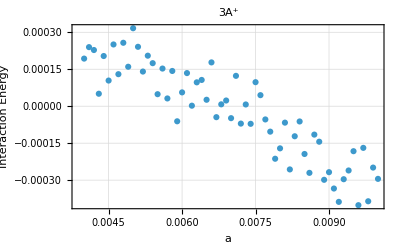

{{0.004,0.000193175},{0.0041,0.000239732},{0.0042,0.000227971},{0.0043,0.0000506023},{0.0044,0.000203628},{0.0045,0.000104123},{0.0046,0.00025057},{0.0047,0.000129963},{0.0048,0.000257393},{0.0049,0.000160105},{0.005,0.000316374},{0.0051,0.000241042},{0.0052,0.000140616},{0.0053,0.000205026},{0.0054,0.000174635},{0.0055,0.0000487895},{0.0056,0.000152806},{0.0057,0.000031512},{0.0058,0.000142999},{0.0059,-0.0000611811},{0.006,0.000056123},{0.0061,0.000134423},{0.0062,2.12506×10^-6},{0.0063,0.0000968743},{0.0064,0.000106585},{0.0065,0.0000261839},{0.0066,0.000177776},{0.0067,-0.0000444672},{0.0068,7.62901×10^-6},{0.0069,0.0000231431},{0.007,-0.0000485197},{0.0071,0.000123193},{0.0072,-0.0000705179},{0.0073,7.07012×10^-6},{0.0074,-0.0000714326},{0.0075,0.0000975356},{0.0076,0.0000448451},{0.0077,-0.0000536712},{0.0078,-0.000103178},{0.0079,-0.000213154},{0.008,-0.000170982},{0.0081,-0.000066671},{0.0082,-0.000256518},{0.0083,-0.000121904},{0.0084,-0.000061888},{0.0085,-0.000193862},{0.0086,-0.0002704},{0.0087,-0.000115181},{0.0088,-0.000144043},{0.0089,-0.000298603},{0.009,-0.000267666},{0.0091,-0.000333988},{0.0092,-0.000388134},{0.0093,-0.000296219},{0.0094,-0.00026077},{0.0095,-0.000182526},{0.0096,-0.000401557},{0.0097,-0.000169023},{0.0098,-0.0003857},{0.0099,-0.000249022},{0.01,-0.000294767}}

```mathematica
a=Range[0.0040,0.0100,0.0001];

d=0.5;u=3000;v:=RandomReal[{-d,d},u];
q=20;p=u+q;

SeedRandom[1,Method->"Rule30CA"];

f3ApData[a_]:=Mean[MapThread[Dot,{#,RotateRight/@#}&[Drop[f3Ap[a,v,p],q]]]/u]/2;

t1=Date[]
f3ApDataA=Thread[{#,ParallelMap[f3ApData,#]}]&[a];
t2=Date[]

Print[((t2[[-3]]-t1[[-3]])*60*60+(t2[[-2]]-t1[[-2]])*60+(t2[[-1]]-t1[[-1]]))/60," minutes"];

ListPlot[f3ApDataA,Frame->True,PlotLabel->"3A^+",FrameLabel->{"a","Interaction Energy"},GridLines->Automatic]

f3ApDataA
```